rotate left and right is for the algebra/list
rotate is for geometry
rotation matrix

```mathematica
RotateLeft[{a,b,c,d}]
```

{b,c,d,a}

```mathematica
RotationMatrix[angle]
```

{{Cos[angle],-Sin[angle]},{Sin[angle],Cos[angle]}}

```mathematica
RotationMatrix[a]//MatrixForm
```

(Cos[a] | -Sin[a]
Sin[a] | Cos[a])

```mathematica
{a,b}.{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}
```

{a Cos[a]+b Sin[a],b Cos[a]-a Sin[a]}

```mathematica
Graphics
[Point[{1,0}],Frame->True,GridLines->Automatic]
```

Graphics

```mathematica
Manipulate[Graphics[{Red,Point[{1,1}],Blue,Point[{1,1}.{{Cos[angle],-Sin[angle]},{Sin[angle],Cos[angle]}}]},Frame->True,PlotRange->{{-2,2},{-2,2}},GridLines->Automatic],{angle,-Pi,Pi}]
```

```mathematica
Dot[{1,1},{{Cos[angle],-Sin[angle]},{Sin[angle],Cos[angle]}}]//MatrixForm
```

(Cos[angle]+Sin[angle]
Cos[angle]-Sin[angle])

```mathematica
Dot[{1,1},{{Cos[0],-Sin[0]},{Sin[0],Cos[0]}}]//MatrixForm
```

(1
1)

#### 不同的变换操作都可以转换为矩形变换。

```mathematica
EulerMatrix/RollPitchYawMatrix/ShearingMatrix/看定义
```

EulerMatrix/(看定义 RollPitchYawMatrix ShearingMatrix)

```mathematica
Manipulate[Graphics[GeometricTransformation[Rectangle[],ShearingMatrix[angle,{1,0},{0,1}]],Frame->True,PlotRange->{{-2,2},{-2,2}}],{angle,-Pi,Pi}]
```

```mathematica
今天的内容
```

今天的内容

```mathematica
RotateBlackWhiteStrips
```

RotateBlackWhiteStrips

```mathematica
Clear[RotateBlackWhiteStrips]
```

```mathematica
RotateBlackWhiteStrips[armed_Integer?((#>3&&EvenQ[#])&),numberOfPoints_Integer?(#>3&),rotation_,color_]:=Graphics[MapIndexed[{If[(-1)^(Plus@@#2)==1,GrayLevel[0],GrayLevel[color]],(*make polygons *)Polygon[Join[#1[[1]],Reverse[#1[[2]]]]]}&,Partition[Partition[(*Calculate Verticers*)Distribute[{N[{{+Cos[#],Sin[#]},{-Sin[#],Cos[#]}}]&/@Range[0,2Pi,2Pi/armed],N[(-1(#/(2Pi)))*{Cos[rotation*#],Sin[rotation*#]}]&/@Range[0,2Pi,2Pi/numberOfPoints]},List,List,List,Dot],numberOfPoints+1],{2,2},1],{2}],AspectRatio->Automatic,PlotRange->All]
```

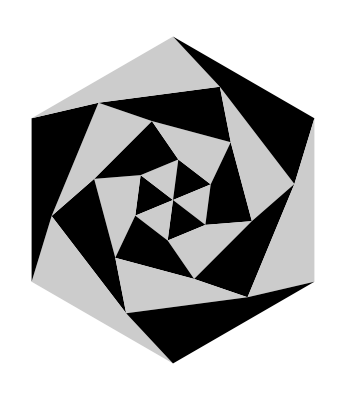

```mathematica
RotateBlackWhiteStrips[6,4,1/4,0.8]
```

```mathematica
Manipulate[bbb=RotateBlackWhiteStrips[i,j,1/k,color],{i,4,20,2},{j,4,20,1},{k,1,20},{color,0,1}]
```

```mathematica
FullForm[bbb];
```

```mathematica
FullForm[bbb]/.Polygon[a__]->a;
fefref=%/.GrayLevel[a_]->Sequence[];
Flatten[fefref[[1,1]],3];
Graphics[Point/@%]
```

-Graphics-

```mathematica
Export["test.csv",Flatten[fefref[[1,1]],3]]
```

test.csv

```mathematica
"test.csv"
```

test.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.csv"]]]
```

```mathematica
Partition[{{0,1},{1,1},{1,0},{0,1}},2,1]
```

{{{0,1},{1,1}},{{1,1},{1,0}},{{1,0},{0,1}}}

```mathematica
aaaa=Table[{RandomInteger[{1,10}],RandomInteger[{1,10}]},20]
```

{{6,2},{7,8},{9,4},{10,2},{6,3},{9,3},{9,3},{9,7},{3,1},{6,1},{4,5},{5,8},{2,8},{8,7},{10,3},{8,3},{7,5},{10,2},{3,1},{3,6}}

```mathematica
aaaa[[1]]
```

{6,2}

```mathematica
bbbb=Append[Partition[aaaa,2,1],aaaa[[1]]]
```

{{{6,2},{7,8}},{{7,8},{9,4}},{{9,4},{10,2}},{{10,2},{6,3}},{{6,3},{9,3}},{{9,3},{9,3}},{{9,3},{9,7}},{{9,7},{3,1}},{{3,1},{6,1}},{{6,1},{4,5}},{{4,5},{5,8}},{{5,8},{2,8}},{{2,8},{8,7}},{{8,7},{10,3}},{{10,3},{8,3}},{{8,3},{7,5}},{{7,5},{10,2}},{{10,2},{3,1}},{{3,1},{3,6}},{6,2}}

```mathematica
Graphics[Line/@bbbb]
```

-Graphics-

## 关于distribute

```mathematica
Distribute[{{22,33,44},{a,b,c}},List,List,List,Dot]
```

{22.a,22.b,22.c,33.a,33.b,33.c,44.a,44.b,44.c}

```mathematica
Distribute[f[{a,b},{c,d,e}],g]
```

g[f[{a,b},{c,d,e}]]

#### 延迟赋值

```mathematica
x=RandomColor[];
{x,x,x,x,x,x,x}
```

{RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624],RGBColor[0.7111931818218746, 0.2832175404562478, 0.037345863262970624]}

```mathematica
x:=RandomColor[];
{x,x,x,x,x,x,x}
```

{RGBColor[0.8508582812048155, 0.43135877363031017, 0.6860468578386507],RGBColor[0.5703736106606603, 0.3758826508324693, 0.13525357852874187],RGBColor[0.07116738334940131, 0.8736209492399476, 0.6733101256204608],RGBColor[0.2752279212974358, 0.4940857134188703, 0.1468649843497185],RGBColor[0.7248685778912072, 0.419822589617898, 0.5646999829942496],RGBColor[0.15838675416436931, 0.8937843255722204, 0.42664676327878204],RGBColor[0.9997305317297798, 0.40684343568744064, 0.9149318832117963]}

```mathematica
Clear[x]
{x,x,x,x}/.x->RandomReal[]
```

{0.57076,0.57076,0.57076,0.57076}

```mathematica
{x,x,x,x}/.x:>RandomReal[]
```

{0.124581,0.801611,0.926845,0.131693}

#### /@ 和 @@ 的区别

```mathematica
Apply[And,{a,b,c,d}]
```

a&&b&&c&&d

```mathematica
Apply[Plus,{a,b,c,d}]
```

a+b+c+d

```mathematica
Map[Plus,{a,b,c,d}]
```

{a,b,c,d}

#### 关于去括号sequence

```mathematica
Dot[Sequence@@#]&/@{{a,b},{c,d},{e,f},{g,h}}
```

{a.b,c.d,e.f,g.h}

```mathematica
Plus[a,b,c]
```

a+b+c

```mathematica
Plus[{a,b,c}]
```

{a,b,c}

```mathematica
Plus[Sequence[a,b,c]]
```

a+b+c

#### module和block的区别

```mathematica
t=10;
```

```mathematica
Module[{t},t]
```

t$4701

```mathematica
Block[{t},t]
```

10

```mathematica
Module[{t=22},t]
```

22

```mathematica
t
```

10

```mathematica
Block[{t=22},t]
```

22

```mathematica
t
```

10

#### foldlist的介绍

```mathematica
FoldList[f,x,{a,b,c,d}]
```

{x,f[x,a],f[f[x,a],b],f[f[f[x,a],b],c],f[f[f[f[x,a],b],c],d]}

```mathematica
FoldList[f,{a,b,c,d}]
```

{a,f[a,b],f[f[a,b],c],f[f[f[a,b],c],d]}

#### nestlist的介绍

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

#### foldlist和nestlist的区别是nestlist的函数输入一个值，而foldlist输入两个值。nestlist输入的是初始值和循环次数，每次都是以上一次的结果作为自变量。而foldlist的函数本身要输入两个值。它新输入的值时刻在变，所以是输入一个初始值和一个接下来的值的列表。